```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin active addresses: bitinfocharts.com.

- Bitcoin market capitalization: bitinfocharts.com.

- Bitcoin hourly price: Bitcoin historical data - kaggle.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2021 bubble).

```mathematica
base=DirectoryName[NotebookFileName[]];
firstPrice="2012-01-01";
lastPrice="2021-03-31";
```

```mathematica
(* Compute Recent Log market cap data: *)
(* Prices list. Pre-processed for performance: *)
hourlyPricesList = Import[base<>"Bitcoin_price-hourly-"<>StringDelete[firstPrice, "-"]<>"-"<>StringDelete[lastPrice, "-"]<>".csv"]
```

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data *)
supply = Import[base<>"Bitcoin_circulating_supply-"<>StringDelete[firstPrice, "-"]<>"-"<>StringDelete[lastPrice, "-"]<>".csv", HeaderLines->1];
```

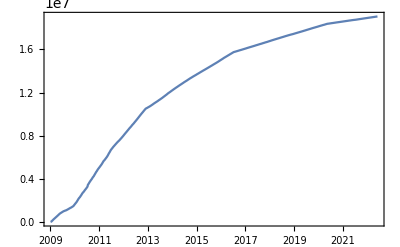

```mathematica
DateListPlot[supply]
```

```mathematica
(* Convert to Unix timestamp: *)
supplyTimestamps = {UnixTime[ToString[#[[1]]]], #[[2]]}&/@supply;
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Interpolation[supplyTimestamps]
```

InterpolatingFunction[…]

```mathematica
{supplyFunction[hourlyPricesList[[1]][[1]]], supplyFunction[hourlyPricesList[[-1]][[1]]]}
```

{7.99789×10^6,1.86692×10^7}

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPricesList
```

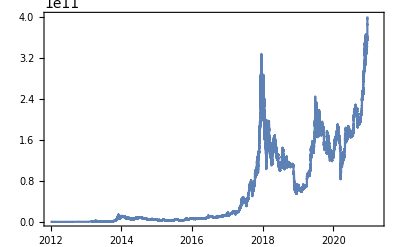

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2015 / 2018 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2015-01-01", "2017-10-18"}, {"2019-11-25", "2021-02-15"}} (* From 2015 / ~2020 to 2 months before the turning point *)
```

{{2015-01-01,2017-10-18},{2019-11-25,2021-02-15}}

```mathematica
n=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1420066800,1508281200},{1574636400,1613343600}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{1021,448}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, n}];
#[[1]]&/@bubbles
```

{{1420066800,22.1981},{1574636400,25.5582}}

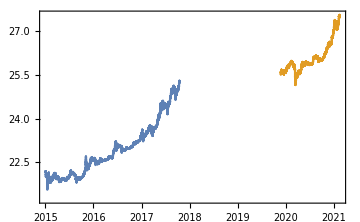

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.00282,0.989321},{1.00102,0.995845}}

```mathematica
Length/@bubblesScaled
```

{24398,10749}

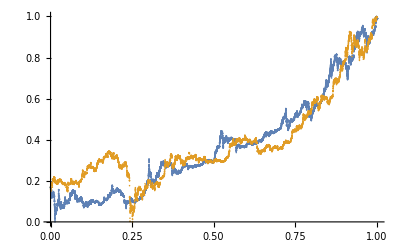

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* 1.b Set up cross validation loop: *)
bandwidthSeq=Range[3, 10, 1]
```

{3,4,5,6,7,8,9,10}

```mathematica
k=10;
```

```mathematica
folds = RandomChoice[Range[k], Length[#]]&/@bubblesScaled
```

```mathematica
cvErrorMtrx = ConstantArray["NA", {Length[bandwidthSeq], k}];
cvErrorMtrx//MatrixForm
```

(NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA)

```mathematica
(* Use Loess: *)
Loess=.
LoessR=ResourceFunction["Loess"]
```

```mathematica
(* FIXME: Currently processing only for 2nd bubble: *)
bubble=2;
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* 1.c Nested for loop. Slow (shortcut below) *)
maxDist=Max[bubbleScaled[[All, 1]]]-Min[bubbleScaled[[All, 1]]];
For[i=1,i<=Length[bandwidthSeq],i++,{Print["i: ",i];For[j=1, j<= k, j++,{
Print["  j: ",j];
fit =bubbleScaled[[Select[Range[Length[bubbleScaled]], folds[[bubble]][[#]]!= j&]]];
pred=bubbleScaled[[Select[Range[Length[bubbleScaled]], folds[[bubble]][[#]]== j&]]];
	preds = LoessR[fit, bandwidthSeq[[i]], pred[[All, 1]], {InterpolationOrder-> 2,"WeightsFunction"-> ((1-(Norm[#]/maxDist)^3)^3&) }];
cvErrorMtrx[[i]][[j]]=Mean[(pred[[All, 2]]-preds)^2];
}]}]
```

i: 1

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 2

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 3

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 4

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 5

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 6

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 7

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 8

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

```mathematica
(* 4. Calculate cross-validation mean square error for each fold: *)
cvErrors=Map[Mean, cvErrorMtrx]
```

{4.8421×10^-6,3.9697×10^-6,4.52735×10^-6,4.73403×10^-6,5.20977×10^-6,5.64765×10^-6,6.03136×10^-6,6.54441×10^-6}

```mathematica
bestIndex=SortBy[Table[{i, cvErrors[[i]]},{i, 1, Length[cvErrors]}], Last][[1]][[1]]
```

2

```mathematica
bestBandwidth=bandwidthSeq[[bestIndex]]
```

4

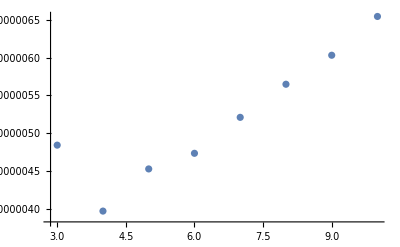

```mathematica
(* Plot results: *)
ListPlot[MapThread[{#1, #2}&, {bandwidthSeq, cvErrors}]]
```

```mathematica
(* Shortcut: *)
bestBandwidth = 4
```

4

```mathematica
bestFits = LoessR[#, bestBandwidth, #[[All, 1]]]&/@bubblesScaled;
```

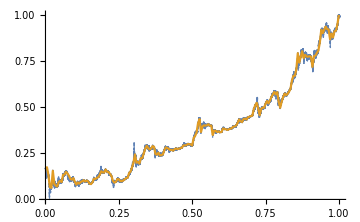
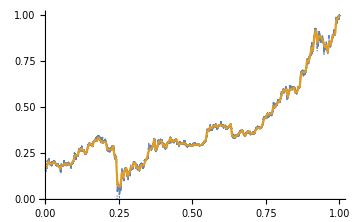

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, bestBandwidth, t]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, n}]
```

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Models=FindProcessParameters[#,ar1Process]&/@ℛs
```

{{ρ→-0.174263,σ→-0.000769467,μ→3.47043×10^-6},{ρ→-0.195667,σ→-0.00131547,μ→-2.98176×10^-7}}

```mathematica
(*Compute the log-likelihood of the fit*)
estimatedProcesses=ar1Process/.#&/@estimatedAR1Models
logLikelihoods=Table[LogLikelihood[estimatedProcesses[[i]],ℛs[[i]]], {i, Length[bubbles]}]
```

{ARProcess[3.47043×10^-6,{-0.174263},5.9208×10^-7],ARProcess[-2.98176×10^-7,{-0.195667},1.73045×10^-6]}

{140310.,56052.}

```mathematica
(* Step 2: Characterize error variance. *)
```

```mathematica
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
(* Allowing for the distribution of the residual standard error on different window sizes to be approximated by Monte Carlo. *)
nPointss=Length/@ℛs;
nSims=100;
sims=Table[RandomFunction[estimatedProcesses[[i]],{0,nPointss[[i]]-1},nSims], {i, n}];
```

```mathematica
ℛsPlots=Table[MapThread[{#1,#2}&,{Range[0,nPointss[[i]]-1],ℛs[[i]][[;;nPointss[[i]]]]}], {i, n}];
```

```mathematica
paths=#["Paths"]&/@sims;
```

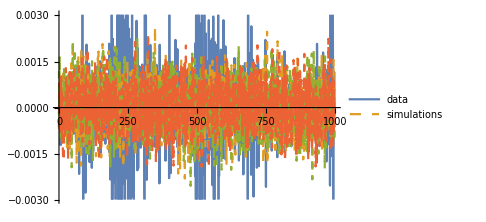
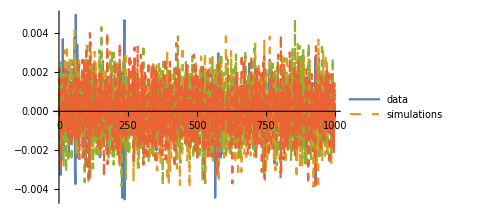

```mathematica
(* Show some simulations and data points *)
showPoints=1000;
showSims=3;
Table[ListLinePlot[Join[{ℛsPlots[[i]][[;;showPoints]]}, paths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,n}]
```

```mathematica
(* Characterize error variance *)
(* The mean squared error of the sample: *)
Mean[#^2]& /@ ℛs
```

{6.10631×10^-7,1.79934×10^-6}

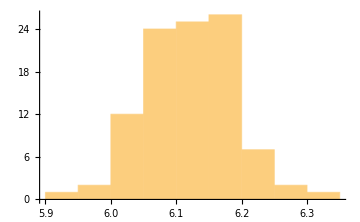
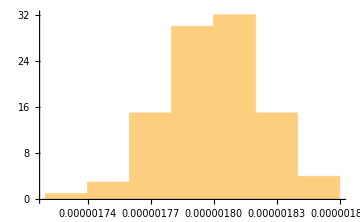

```mathematica
(* The mean squared errors of the simulations: *)
meanErrors=Table[Map[Mean[(#[[All,2]])^2]&,paths[[i]]], {i, n}];
Histogram[#, ImageSize->Medium]&/@meanErrors
```

```mathematica
(* The mean of the mean errors *)
meanMeanErrors=Mean/@meanErrors
```

{6.11961×10^-7,1.79944×10^-6}

```mathematica
(* The variance of the mean errors *)
varianceMeanErrors=Variance/@meanErrors
```

{4.48714×10^-17,5.05148×10^-16}

```mathematica
(* The standard deviation of the mean errors *)
stdDevMeanErrors=StandardDeviation/@meanErrors
```

{6.69861×10^-9,2.24755×10^-8}

```mathematica
(* Mean errors 95% C.I. (probably not correct, because of the auto-correlated residuals): *)
ciMeanErrors=Table[meanMeanErrors[[i]]+1.96 stdDevMeanErrors[[i]], {i, n}]
```

{6.2509×10^-7,1.84349×10^-6}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Profiling over 0.1 < m < 0.5, 7 < ω < 14 and 1. < tc < 1.2 *)
(* Try to estimate all the params using log-likelihood: *)
(* Use the second bubble: *)
bubble=2
bubbleScaled=bubblesScaled[[bubble]];
```

2

```mathematica
(* Define two months in the future scaled interval endpoint: *)
maxTc=(bubblesDays[[bubble]]+60)/bubblesDays[[bubble]]//N
```

1.13393

```mathematica
(* Define 1 week resolution scaled interval step: *)
stepTc=7/bubblesDays[[bubble]]//N
```

0.015625

```mathematica
(* Define 1 month resolution scaled initial time step *)
stepTi=30/bubblesDays[[bubble]]//N
```

0.0669643

```mathematica
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[Table[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
Total[#^2&/@ℛ]/(Length[ℛ]-numParams),
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,0.1,0.5,1./10}, {ω,7.,14.,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], LL-> bestFit[[7]], ℛerror-> bestFit[[6]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

{1585.29,{{a→3.4641,b→-3.31685,c→0.0485209,d→-0.0124953,T_1→0.,tc→1.06362,m→0.1,ω→9.5,LL→47794.,ℛerror→0.00364428,ρ→0.998887,σ→-0.00284657,μ→1.55341×10^-18},{a→3.65837,b→-3.51463,c→0.0468705,d→-0.0209445,T_1→0.0669643,tc→1.07925,m→0.1,ω→10.3,LL→44432.7,ℛerror→0.00397547,ρ→0.998943,σ→-0.00289784,μ→3.36988×10^-18},{a→3.51972,b→-3.38058,c→0.0425042,d→-0.016524,T_1→0.133929,tc→1.06362,m→0.1,ω→9.6,LL→41050.3,ℛerror→0.00402296,ρ→0.998887,σ→-0.00298992,μ→-1.40014×10^-18},{a→3.53897,b→-3.43017,c→0.0163976,d→-0.0156858,T_1→0.200893,tc→1.048,m→0.1,ω→9.7,LL→37555.3,ℛerror→0.00315064,ρ→0.998213,σ→-0.00335233,μ→1.36382×10^-18},{a→3.59931,b→-3.50214,c→0.00954423,d→0.0308258,T_1→0.267857,tc→1.048,m→0.1,ω→8.4,LL→35719.2,ℛerror→0.00221461,ρ→0.998476,σ→-0.00259605,μ→2.9208×10^-18},{a→2.08881,b→-2.02055,c→-0.00588901,d→0.0397117,T_1→0.334821,tc→1.048,m→0.2,ω→8.1,LL→32471.4,ℛerror→0.00257755,ρ→0.998705,σ→-0.00258152,μ→1.72666×10^-18},{a→1.98742,b→-1.91808,c→0.0174114,d→0.00592724,T_1→0.401786,tc→1.03237,m→0.2,ω→13.6,LL→29283.2,ℛerror→0.00273484,ρ→0.998741,σ→-0.00262174,μ→2.38001×10^-19},{a→1.61693,b→-1.65086,c→0.0490738,d→0.048917,T_1→0.46875,tc→1.03237,m→0.3,ω→7.7,LL→25835.4,ℛerror→0.00181554,ρ→0.997956,σ→-0.00272094,μ→3.60032×10^-19},{a→2.0147,b→-2.10125,c→0.0118306,d→-0.0861409,T_1→0.535714,tc→1.09487,m→0.3,ω→11.5,LL→22304.,ℛerror→0.00148416,ρ→0.997326,σ→-0.0028135,μ→2.63201×10^-19}}}

```mathematica
fits[[2]][[All,6]]
```

{tc→1.06362,tc→1.07925,tc→1.06362,tc→1.048,tc→1.048,tc→1.048,tc→1.03237,tc→1.03237,tc→1.09487}

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

26.4215

```mathematica
(* Average tc: *)
meanTc=Total[fits[[2]][[All,6]][[All,2]]]/Length[fits[[2]]]
```

1.05668

```mathematica
minTc=Min[fits[[2]][[All,6]][[All,2]]]
maxTc=Max[fits[[2]][[All,6]][[All,2]]]
```

1.03237

1.09487

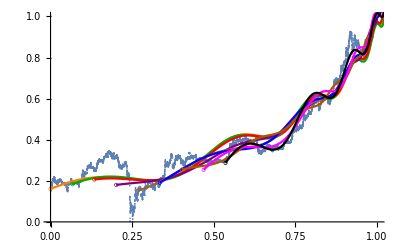

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[2]][[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits[[2]]]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[2]][[i+1]]],""], {i,0,Length[fits[[2]]]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* By definition, the best fit is the one with smallest variance: *)
fit=MinimalBy[Table[{fits[[2]][[i]], index-> i}, {i,Length[fits[[2]]]}], (#[[1]][[12]][[2]])^2&]//Flatten
```

{a→2.08881,b→-2.02055,c→-0.00588901,d→0.0397117,T_1→0.334821,tc→1.048,m→0.2,ω→8.1,LL→32471.4,ℛerror→0.00257755,ρ→0.998705,σ→-0.00258152,μ→1.72666×10^-18,index→6}

```mathematica
bestIndex=fit//Last//Part[#,2]&
```

6

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* First do lower leg (most useful one) of the tc CI: *)
(* Slowly reduce tc until the log-likelihood test is 1.92 points below the maximum LL.
First version: Re-fit the linear parameters, keeping the non-linear ones fixed: *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.2

8.1

1.048

32471.4

```mathematica
t1=Subscript[T, 1]/.fit;
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&]
```

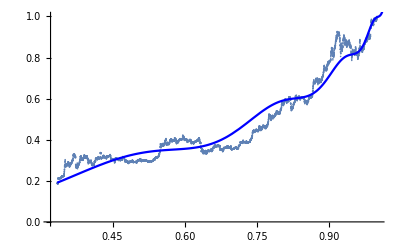

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→2.08881,b→-2.02055,c→-0.00588901,d→0.0397117,T_1→0.334821,tc→1.048,m→0.2,ω→8.1,LL→32471.4,ℛerror→0.00257755,ρ→0.998705,σ→-0.00258152,μ→1.72666×10^-18,index→6}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest]
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
```

```mathematica
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.998705,σ→-0.00258152,μ→1.72666×10^-18}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals: *)
lowCItc=bestTc-10/1251;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]
bestLL-lowCILL
```

32469.5

1.9232

```mathematica
{lowCItc, bestTc}
```

{1.04001,1.048}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc+10/1326;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]
bestLL-highCILL
```

32469.5

1.92045

```mathematica
{lowCItc, bestTc, highCItc}
```

{1.04001,1.048,1.05554}

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc]
```

Thu 4 Mar 2021 22:08:21

```mathematica
(* Now compute the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc]
```

Thu 11 Mar 2021 21:10:20

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc]
```

Mon 8 Mar 2021 12:05:11

```mathematica
(* This is the date of the actual bubble popping: *)
DatePlus[bubblesDate[[bubble]][[2]], 58]
```

Wed 14 Apr 2021 00:00:00

```mathematica
(* :-/ *)
```

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc]
```

Fri 12 Mar 2021 09:25:11

```mathematica
(* Slightly better *)
```

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc]
```

Mon 29 Mar 2021 12:05:11

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc]
```

Mon 1 Mar 2021 12:05:11

```mathematica
(* For reference: *)
{#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]]}&/@fits[[2]]//TableForm
```

tc→1.06362 | Mon 15 Mar 2021 12:05:11
tc→1.07925 | Mon 22 Mar 2021 12:05:11
tc→1.06362 | Mon 15 Mar 2021 12:05:11
tc→1.048 | Mon 8 Mar 2021 12:05:11
tc→1.048 | Mon 8 Mar 2021 12:05:11
tc→1.048 | Mon 8 Mar 2021 12:05:11
tc→1.03237 | Mon 1 Mar 2021 12:05:11
tc→1.03237 | Mon 1 Mar 2021 12:05:11
tc→1.09487 | Mon 29 Mar 2021 12:05:11